# Bootstrapping v4.0 (smh)

## I mean at some point I am bound to get this right

```mathematica
ModuleDirectory = NotebookDirectory[] <> "../modules/";
<< (ModuleDirectory<> "debugTools.wl");
<< (ModuleDirectory<> "dataLoader.wl");
<< (ModuleDirectory<> "bootstraptdl.wl");
<< (ModuleDirectory<> "defect.wl");
```

math4ti2: Mathematica interface to 4ti2 (http://www.4ti2.de/)
Copyright (C) 2017, Ralf Hemmecke <ralf@hemmecke.org>
Copyright (C) 2017, Silviu Radu <sradu@risc.jku.at>

```mathematica
?dataLoader`*
```

```mathematica
(* Calculate Boundaries in C and Pull back to TIM^2 *)
Module[
{md,s, z, t,boundaries, defects, x, xz, pullbacks,untwisted,transmission,S,T,Z,weights,indices},
md=ModularDataFoldMinimal[];
s=Get@FileNameJoin[{NotebookDirectory[],"m-dcoset-sp6-S.m"}];
t=Get@FileNameJoin[{NotebookDirectory[],"m-dcoset-sp6-T.m"}];
weights=Get@FileNameJoin[{NotebookDirectory[],"m-dcoset-sp6-conformal-weights.m"}];
weights//Echo;

(* The defects in here to find the inverse Z2 *)
defects= #/#[[1]] & /@ s//Simplify//Transpose;

boundaries = #/Sqrt[#[[1]]] & /@ s//Simplify//Transpose;

transmission=(a|->(1-#[[a]]/#[[1]])/2&/@boundaries )/@Range[Length@boundaries] ;
transmission//N//Echo;
]//Time
```

{0,1/3,5/6,3/2,3/2,2,7/120,69/40,19/40,127/120,13/5,14/15,43/30,31/10,1/10,3/5,59/24,1/8,7/8,59/24,7/120,69/40,19/40,127/120,7/10,1/30,8/15,6/5,1/5,7/10,79/120,13/40,3/40,79/120,31/10,43/30,14/15,13/5,3/5,1/10}

{{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.326446,0.1975,0.1975,-0.326446,0.721445,0.721445,0.1975,1.105,0.5,0.1975,-0.326446,0.1975,0.1975,-0.326446,0.721445,0.721445,0.1975,1.105,0.5,0.1975,0.1975,1.105,0.5,0.1975,-0.326446,0.1975,0.1975,-0.326446,0.721445,0.721445,0.1975,1.105,0.5,0.1975,-0.326446,0.1975,0.1975,-0.326446,0.721445,0.721445},{-0.326446,0.1975,0.1975,-0.326446,0.721445,0.721445,0.8025,-0.105,0.5,0.8025,-0.326446,0.1975,0.1975,-0.326446,0.721445,0.721445,0.8025,-0.105,0.5,0.8025,0.8025,-0.105,0.5,0.8025,-0.326446,0.1975,0.1975,-0.326446,0.721445,0.721445,0.8025,-0.105,0.5,0.8025,-0.326446,0.1975,0.1975,-0.326446,0.721445,0.721445},{0.,0.,0.,0.,0.,0.,1.,1.,1.,1.,0.,0.,0.,0.,0.,0.,1.,1.,1.,1.,1.,1.,1.,1.,0.,0.,0.,0.,0.,0.,1.,1.,1.,1.,0.,0.,0.,0.,0.,0.},{-0.465926,0.758819,0.758819,-0.465926,0.43065,0.43065,0.241181,0.241181,0.758819,0.241181,-0.465926,0.758819,0.758819,-0.465926,0.43065,0.43065,0.241181,0.241181,0.758819,0.241181,0.241181,0.241181,0.758819,0.241181,-0.465926,0.758819,0.758819,-0.465926,0.43065,0.43065,0.241181,0.241181,0.758819,0.241181,-0.465926,0.758819,0.758819,-0.465926,0.43065,0.43065},{-0.465926,0.758819,0.758819,-0.465926,0.43065,0.43065,0.758819,0.758819,0.241181,0.758819,-0.465926,0.758819,0.758819,-0.465926,0.43065,0.43065,0.758819,0.758819,0.241181,0.758819,0.758819,0.758819,0.241181,0.758819,-0.465926,0.758819,0.758819,-0.465926,0.43065,0.43065,0.758819,0.758819,0.241181,0.758819,-0.465926,0.758819,0.758819,-0.465926,0.43065,0.43065},{-0.551255,0.115214,0.884786,1.55126,0.218317,0.781683,0.245431,0.5,0.5,0.754569,0.901544,0.646975,0.353025,0.0984562,0.607593,0.392407,1.16647,0.5,0.5,-0.166469,-0.166469,0.5,0.5,1.16647,0.0984562,0.353025,0.646975,0.901544,0.392407,0.607593,0.754569,0.5,0.5,0.245431,1.55126,0.884786,0.115214,-0.551255,0.781683,0.218317},{-0.551255,1.26957,-0.269572,1.55126,0.218317,0.781683,0.5,0.5,0.5,0.5,0.901544,0.20605,0.79395,0.0984562,0.607593,0.392407,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.0984562,0.79395,0.20605,0.901544,0.392407,0.607593,0.5,0.5,0.5,0.5,1.55126,-0.269572,1.26957,-0.551255,0.781683,0.218317},{-0.88353,0.5,0.5,1.88353,0.870716,0.129284,0.5,0.5,0.5,0.5,1.02846,0.5,0.5,-0.0284614,0.358399,0.641601,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,-0.0284614,0.5,0.5,1.02846,0.641601,0.358399,0.5,0.5,0.5,0.5,1.88353,0.5,0.5,-0.88353,0.129284,0.870716},{-0.551255,0.115214,0.884786,1.55126,0.218317,0.781683,0.754569,0.5,0.5,0.245431,0.901544,0.646975,0.353025,0.0984562,0.607593,0.392407,-0.166469,0.5,0.5,1.16647,1.16647,0.5,0.5,-0.166469,0.0984562,0.353025,0.646975,0.901544,0.392407,0.607593,0.245431,0.5,0.5,0.754569,1.55126,0.884786,0.115214,-0.551255,0.781683,0.218317},{-0.13601,-0.13601,-0.13601,-0.13601,-0.13601,-0.13601,0.742934,0.742934,0.742934,0.742934,0.742934,0.742934,0.742934,0.742934,0.742934,0.742934,-0.13601,-0.13601,-0.13601,-0.13601,-0.13601,-0.13601,-0.13601,-0.13601,0.742934,0.742934,0.742934,0.742934,0.742934,0.742934,0.742934,0.742934,0.742934,0.742934,-0.13601,-0.13601,-0.13601,-0.13601,-0.13601,-0.13601},{-0.551255,0.115214,0.115214,-0.551255,0.781683,0.781683,0.646975,0.20605,0.5,0.646975,0.901544,0.646975,0.646975,0.901544,0.392407,0.392407,0.115214,1.26957,0.5,0.115214,0.115214,1.26957,0.5,0.115214,0.901544,0.646975,0.646975,0.901544,0.392407,0.392407,0.646975,0.20605,0.5,0.646975,-0.551255,0.115214,0.115214,-0.551255,0.781683,0.781683},{-0.551255,0.115214,0.115214,-0.551255,0.781683,0.781683,0.353025,0.79395,0.5,0.353025,0.901544,0.646975,0.646975,0.901544,0.392407,0.392407,0.884786,-0.269572,0.5,0.884786,0.884786,-0.269572,0.5,0.884786,0.901544,0.646975,0.646975,0.901544,0.392407,0.392407,0.353025,0.79395,0.5,0.353025,-0.551255,0.115214,0.115214,-0.551255,0.781683,0.781683},{-0.13601,-0.13601,-0.13601,-0.13601,-0.13601,-0.13601,0.257066,0.257066,0.257066,0.257066,0.742934,0.742934,0.742934,0.742934,0.742934,0.742934,1.13601,1.13601,1.13601,1.13601,1.13601,1.13601,1.13601,1.13601,0.742934,0.742934,0.742934,0.742934,0.742934,0.742934,0.257066,0.257066,0.257066,0.257066,-0.13601,-0.13601,-0.13601,-0.13601,-0.13601,-0.13601},{-0.728677,0.829223,0.829223,-0.728677,0.411785,0.411785,0.625752,0.625752,0.374248,0.625752,0.969313,0.374248,0.374248,0.969313,0.533695,0.533695,0.170777,0.170777,0.829223,0.170777,0.170777,0.170777,0.829223,0.170777,0.969313,0.374248,0.374248,0.969313,0.533695,0.533695,0.625752,0.625752,0.374248,0.625752,-0.728677,0.829223,0.829223,-0.728677,0.411785,0.411785},{-0.728677,0.829223,0.829223,-0.728677,0.411785,0.411785,0.374248,0.374248,0.625752,0.374248,0.969313,0.374248,0.374248,0.969313,0.533695,0.533695,0.829223,0.829223,0.170777,0.829223,0.829223,0.829223,0.170777,0.829223,0.969313,0.374248,0.374248,0.969313,0.533695,0.533695,0.374248,0.374248,0.625752,0.374248,-0.728677,0.829223,0.829223,-0.728677,0.411785,0.411785},{-0.326446,0.1975,0.8025,1.32645,0.278555,0.721445,1.02395,0.5,0.5,-0.0239457,-0.326446,0.1975,0.8025,1.32645,0.278555,0.721445,1.02395,0.5,0.5,-0.0239457,-0.0239457,0.5,0.5,1.02395,1.32645,0.8025,0.1975,-0.326446,0.721445,0.278555,-0.0239457,0.5,0.5,1.02395,1.32645,0.8025,0.1975,-0.326446,0.721445,0.278555},{-0.326446,1.105,-0.105,1.32645,0.278555,0.721445,0.5,0.5,0.5,0.5,-0.326446,1.105,-0.105,1.32645,0.278555,0.721445,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,1.32645,-0.105,1.105,-0.326446,0.721445,0.278555,0.5,0.5,0.5,0.5,1.32645,-0.105,1.105,-0.326446,0.721445,0.278555},{-0.587664,0.5,0.5,1.58766,0.791439,0.208561,0.5,0.5,0.5,0.5,-0.587664,0.5,0.5,1.58766,0.791439,0.208561,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,1.58766,0.5,0.5,-0.587664,0.208561,0.791439,0.5,0.5,0.5,0.5,1.58766,0.5,0.5,-0.587664,0.208561,0.791439},{-0.326446,0.1975,0.8025,1.32645,0.278555,0.721445,-0.0239457,0.5,0.5,1.02395,-0.326446,0.1975,0.8025,1.32645,0.278555,0.721445,-0.0239457,0.5,0.5,1.02395,1.02395,0.5,0.5,-0.0239457,1.32645,0.8025,0.1975,-0.326446,0.721445,0.278555,1.02395,0.5,0.5,-0.0239457,1.32645,0.8025,0.1975,-0.326446,0.721445,0.278555},{-0.551255,0.115214,0.884786,1.55126,0.218317,0.781683,-0.166469,0.5,0.5,1.16647,-0.551255,0.115214,0.884786,1.55126,0.218317,0.781683,-0.166469,0.5,0.5,1.16647,0.245431,0.5,0.5,0.754569,0.0984562,0.353025,0.646975,0.901544,0.392407,0.607593,0.245431,0.5,0.5,0.754569,0.0984562,0.353025,0.646975,0.901544,0.392407,0.607593},{-0.551255,1.26957,-0.269572,1.55126,0.218317,0.781683,0.5,0.5,0.5,0.5,-0.551255,1.26957,-0.269572,1.55126,0.218317,0.781683,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.0984562,0.79395,0.20605,0.901544,0.392407,0.607593,0.5,0.5,0.5,0.5,0.0984562,0.79395,0.20605,0.901544,0.392407,0.607593},{-0.88353,0.5,0.5,1.88353,0.870716,0.129284,0.5,0.5,0.5,0.5,-0.88353,0.5,0.5,1.88353,0.870716,0.129284,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,-0.0284614,0.5,0.5,1.02846,0.641601,0.358399,0.5,0.5,0.5,0.5,-0.0284614,0.5,0.5,1.02846,0.641601,0.358399},{-0.551255,0.115214,0.884786,1.55126,0.218317,0.781683,1.16647,0.5,0.5,-0.166469,-0.551255,0.115214,0.884786,1.55126,0.218317,0.781683,1.16647,0.5,0.5,-0.166469,0.754569,0.5,0.5,0.245431,0.0984562,0.353025,0.646975,0.901544,0.392407,0.607593,0.754569,0.5,0.5,0.245431,0.0984562,0.353025,0.646975,0.901544,0.392407,0.607593},{-0.309017,-0.309017,-0.309017,-0.309017,-0.309017,-0.309017,0.190983,0.190983,0.190983,0.190983,0.809017,0.809017,0.809017,0.809017,0.809017,0.809017,1.30902,1.30902,1.30902,1.30902,0.190983,0.190983,0.190983,0.190983,0.381966,0.381966,0.381966,0.381966,0.381966,0.381966,0.618034,0.618034,0.618034,0.618034,0.809017,0.809017,0.809017,0.809017,0.809017,0.809017},{-0.837217,0.0105444,0.0105444,-0.837217,0.858306,0.858306,0.313045,0.873911,0.5,0.313045,1.01077,0.686955,0.686955,1.01077,0.363139,0.363139,0.989456,-0.478911,0.5,0.989456,0.313045,0.873911,0.5,0.313045,0.304903,0.428589,0.428589,0.304903,0.552276,0.552276,0.571411,0.357179,0.5,0.571411,1.01077,0.686955,0.686955,1.01077,0.363139,0.363139},{-0.837217,0.0105444,0.0105444,-0.837217,0.858306,0.858306,0.686955,0.126089,0.5,0.686955,1.01077,0.686955,0.686955,1.01077,0.363139,0.363139,0.0105444,1.47891,0.5,0.0105444,0.686955,0.126089,0.5,0.686955,0.304903,0.428589,0.428589,0.304903,0.552276,0.552276,0.428589,0.642821,0.5,0.428589,1.01077,0.686955,0.686955,1.01077,0.363139,0.363139},{-0.309017,-0.309017,-0.309017,-0.309017,-0.309017,-0.309017,0.809017,0.809017,0.809017,0.809017,0.809017,0.809017,0.809017,0.809017,0.809017,0.809017,-0.309017,-0.309017,-0.309017,-0.309017,0.809017,0.809017,0.809017,0.809017,0.381966,0.381966,0.381966,0.381966,0.381966,0.381966,0.381966,0.381966,0.381966,0.381966,0.809017,0.809017,0.809017,0.809017,0.809017,0.809017},{-1.0629,0.918778,0.918778,-1.0629,0.387789,0.387789,0.340041,0.340041,0.659959,0.340041,1.09697,0.340041,0.340041,1.09697,0.542861,0.542861,0.918778,0.918778,0.081222,0.918778,0.340041,0.340041,0.659959,0.340041,0.271976,0.561099,0.561099,0.271976,0.483629,0.483629,0.561099,0.561099,0.438901,0.561099,1.09697,0.340041,0.340041,1.09697,0.542861,0.542861},{-1.0629,0.918778,0.918778,-1.0629,0.387789,0.387789,0.659959,0.659959,0.340041,0.659959,1.09697,0.340041,0.340041,1.09697,0.542861,0.542861,0.081222,0.081222,0.918778,0.081222,0.659959,0.659959,0.340041,0.659959,0.271976,0.561099,0.561099,0.271976,0.483629,0.483629,0.438901,0.438901,0.561099,0.438901,1.09697,0.340041,0.340041,1.09697,0.542861,0.542861},{-0.837217,0.0105444,0.989456,1.83722,0.141694,0.858306,0.823816,0.5,0.5,0.176184,1.01077,0.686955,0.313045,-0.0107716,0.636861,0.363139,-0.347762,0.5,0.5,1.34776,0.176184,0.5,0.5,0.823816,0.695097,0.571411,0.428589,0.304903,0.552276,0.447724,0.623687,0.5,0.5,0.376313,-0.0107716,0.313045,0.686955,1.01077,0.363139,0.636861},{-0.837217,1.47891,-0.478911,1.83722,0.141694,0.858306,0.5,0.5,0.5,0.5,1.01077,0.126089,0.873911,-0.0107716,0.636861,0.363139,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.695097,0.357179,0.642821,0.304903,0.552276,0.447724,0.5,0.5,0.5,0.5,-0.0107716,0.873911,0.126089,1.01077,0.363139,0.636861},{-1.25988,0.5,0.5,2.25988,0.971558,0.0284423,0.5,0.5,0.5,0.5,1.17221,0.5,0.5,-0.172213,0.319881,0.680119,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.756763,0.5,0.5,0.243237,0.431201,0.568799,0.5,0.5,0.5,0.5,-0.172213,0.5,0.5,1.17221,0.680119,0.319881},{-0.837217,0.0105444,0.989456,1.83722,0.141694,0.858306,0.176184,0.5,0.5,0.823816,1.01077,0.686955,0.313045,-0.0107716,0.636861,0.363139,1.34776,0.5,0.5,-0.347762,0.823816,0.5,0.5,0.176184,0.695097,0.571411,0.428589,0.304903,0.552276,0.447724,0.376313,0.5,0.5,0.623687,-0.0107716,0.313045,0.686955,1.01077,0.363139,0.636861},{-0.13601,-0.13601,-0.13601,-0.13601,-0.13601,-0.13601,1.13601,1.13601,1.13601,1.13601,-0.13601,-0.13601,-0.13601,-0.13601,-0.13601,-0.13601,1.13601,1.13601,1.13601,1.13601,0.257066,0.257066,0.257066,0.257066,0.742934,0.742934,0.742934,0.742934,0.742934,0.742934,0.257066,0.257066,0.257066,0.257066,0.742934,0.742934,0.742934,0.742934,0.742934,0.742934},{-0.551255,0.115214,0.115214,-0.551255,0.781683,0.781683,0.884786,-0.269572,0.5,0.884786,-0.551255,0.115214,0.115214,-0.551255,0.781683,0.781683,0.884786,-0.269572,0.5,0.884786,0.353025,0.79395,0.5,0.353025,0.901544,0.646975,0.646975,0.901544,0.392407,0.392407,0.353025,0.79395,0.5,0.353025,0.901544,0.646975,0.646975,0.901544,0.392407,0.392407},{-0.551255,0.115214,0.115214,-0.551255,0.781683,0.781683,0.115214,1.26957,0.5,0.115214,-0.551255,0.115214,0.115214,-0.551255,0.781683,0.781683,0.115214,1.26957,0.5,0.115214,0.646975,0.20605,0.5,0.646975,0.901544,0.646975,0.646975,0.901544,0.392407,0.392407,0.646975,0.20605,0.5,0.646975,0.901544,0.646975,0.646975,0.901544,0.392407,0.392407},{-0.13601,-0.13601,-0.13601,-0.13601,-0.13601,-0.13601,-0.13601,-0.13601,-0.13601,-0.13601,-0.13601,-0.13601,-0.13601,-0.13601,-0.13601,-0.13601,-0.13601,-0.13601,-0.13601,-0.13601,0.742934,0.742934,0.742934,0.742934,0.742934,0.742934,0.742934,0.742934,0.742934,0.742934,0.742934,0.742934,0.742934,0.742934,0.742934,0.742934,0.742934,0.742934,0.742934,0.742934},{-0.728677,0.829223,0.829223,-0.728677,0.411785,0.411785,0.829223,0.829223,0.170777,0.829223,-0.728677,0.829223,0.829223,-0.728677,0.411785,0.411785,0.829223,0.829223,0.170777,0.829223,0.374248,0.374248,0.625752,0.374248,0.969313,0.374248,0.374248,0.969313,0.533695,0.533695,0.374248,0.374248,0.625752,0.374248,0.969313,0.374248,0.374248,0.969313,0.533695,0.533695},{-0.728677,0.829223,0.829223,-0.728677,0.411785,0.411785,0.170777,0.170777,0.829223,0.170777,-0.728677,0.829223,0.829223,-0.728677,0.411785,0.411785,0.170777,0.170777,0.829223,0.170777,0.625752,0.625752,0.374248,0.625752,0.969313,0.374248,0.374248,0.969313,0.533695,0.533695,0.625752,0.625752,0.374248,0.625752,0.969313,0.374248,0.374248,0.969313,0.533695,0.533695}}

Time:   0.357071

```mathematica
(* Calculate Boundaries in BAA and Pull back to TIM^2 *)
Module[
{md,s, z, t,boundaries, defects, x, xz, pullbacks,untwisted,transmission,S,T,Z,weights,indices},
md=ModularDataFoldMinimal[];
s=Get@FileNameJoin[{NotebookDirectory[],"AE-maximal-S-matrix.m"}];
t=Get@FileNameJoin[{NotebookDirectory[],"AE-maximal-T-matrix.m"}];
weights=Get@FileNameJoin[{NotebookDirectory[],"AE-maximal-conformal-weights.m"}];

(* The defects in here to find the inverse Z2 *)
defects= #/#[[1]] & /@ s//Simplify//Transpose;

S=Get@FileNameJoin[{NotebookDirectory[],"S-matrix-su2xsu2-over-su2.m"}];
T=Get@FileNameJoin[{NotebookDirectory[],"T-matrix-su2xsu2-over-su2.m"}];
weights=Get@FileNameJoin[{NotebookDirectory[],"conformal-weights-su2xsu2-over-su2.m"}];
Z=Get@FileNameJoin[{NotebookDirectory[],"AE-modular-invariant-su2xsu2-over-su2.m"}];
indices=Get@FileNameJoin[{NotebookDirectory[],"index-convention-su2xsu2-over-su2.m"}];
indices//Echo;

boundaries = #/Sqrt[#[[1]]] & /@ S//Simplify//Transpose;

transmission=(1-#[[17]]/#[[1]])/2&/@boundaries;
transmission//N//Echo;
]//Time
```

{{0,0,0},{0,0,2},{0,0,4},{0,0,6},{0,0,8},{0,0,10},{0,1,1},{0,1,3},{0,1,5},{0,1,7},{0,1,9},{0,2,0},{0,2,2},{0,2,4},{0,2,6},{0,2,8},{0,2,10},{1,0,1},{1,0,3},{1,0,5},{1,0,7},{1,0,9},{1,1,0},{1,1,2},{1,1,4},{1,1,6},{1,1,8},{1,1,10},{1,2,1},{1,2,3},{1,2,5},{1,2,7},{1,2,9},{2,0,0},{2,0,2},{2,0,4},{2,0,6},{2,0,8},{2,0,10},{2,1,1},{2,1,3},{2,1,5},{2,1,7},{2,1,9},{2,2,0},{2,2,2},{2,2,4},{2,2,6},{2,2,8},{2,2,10},{3,0,1},{3,0,3},{3,0,5},{3,0,7},{3,0,9},{3,1,0},{3,1,2},{3,1,4},{3,1,6},{3,1,8},{3,1,10},{3,2,1},{3,2,3},{3,2,5},{3,2,7},{3,2,9},{4,0,0},{4,0,2},{4,0,4},{4,0,6},{4,0,8},{4,0,10},{4,1,1},{4,1,3},{4,1,5},{4,1,5}}

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

Time:   0.368141

```mathematica
(* Calculate Boundaries in BAE and Pull back to TIM^2 *)
Module[
{md,s, z, t,boundaries, defects, x, xz, pullbacks,untwisted,transmission,S,T,Z,weights},
md=ModularDataFoldMinimal[];
s=Get@FileNameJoin[{NotebookDirectory[],"AE-maximal-S-matrix.m"}];
t=Get@FileNameJoin[{NotebookDirectory[],"AE-maximal-T-matrix.m"}];
weights=Get@FileNameJoin[{NotebookDirectory[],"AE-maximal-conformal-weights.m"}];
weights//Echo;

(* The defects in here to find the inverse Z2 *)
defects= #/#[[1]] & /@ s//Simplify//Transpose;

boundaries = #/Sqrt[#[[1]]] & /@ s//Simplify//Transpose;

transmission=(1-#[[5]]/#[[1]])/2&/@boundaries;
transmission//N//Echo;
]//Time
```

{0,3/2,7/8,3/2,2,61/80,21/80,61/80,21/80,6/5,7/10,3/40,7/10,1/5,1/16,9/16,1/16,9/16,3/5,1/10,19/40,19/40}

{0.,0.,0.,0.,0.,1.,1.,1.,1.,0.,0.,0.,0.,0.,1.,1.,1.,1.,0.,0.,0.,0.}

Time:   0.073893

{0,3/80,7/160,1/16,3/40,3/32,1/10,11/80,1/5,21/80,11/32,7/16,19/40,43/80,9/16,19/32,3/5,51/80,7/10,61/80,127/160,27/32,7/8,83/80,43/40,6/5,6/5,207/160,3/2,123/80,247/160,8/5,15/8,31/16,2,21/10,11/5,3,4}

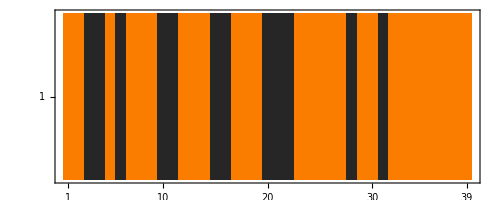

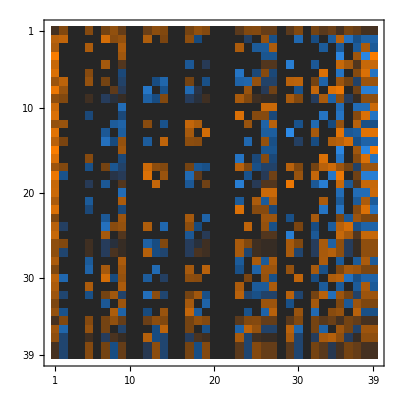

Time:   3.04429

{0,0,1,1,0,1,0,0,0,1,1,0,0,0,1,1,0,0,0,1,1,1,0,0,0,0,0,1,0,0,1,0,0,0,0,0,0,0,0}

```mathematica
(* Calculate Boundaries in TIM^2/Z_2 and Pull back to TIM^2 *)
Module[
{md,s, z, t,boundaries, defects, x, xz, pullbacks,untwisted,transmission},
md=ModularDataFoldZ2OrbifoldMinimal[];
s=md["S"];
t=md["T"];
z=md["Z"];
md["irreps"]["weights"] //Echo;

(* Calculate boundaries *)
boundaries = #/Sqrt[#[[1]]] & /@ s//Simplify//Transpose;
(*boundaries//MatrixPlot//Echo;*)

(* The defects in here to find the inverse Z2 *)
defects= #/#[[1]] & /@ s//Simplify//Transpose;
(*defects//MatrixForm//Echo;*)

(* It looks like there are 3 Z_2's in there in a Z_2^2, 
   so which one is the inverse? 
(probably the diagonal one) *)
x = defects[[-5]];

(* Let's check if it is *)
xz = x*#&/@z;
(z + xz + s . xz . s + t . s . xz . s . ConjugateTranspose[t])/2// N//Chop // MatrixPlot/Echo;
(* Ok it isn't the last one, but it is the one I picked because I now have checked lol *)

(*The pullback is going to be *)
pullbacks = (# + x * #)/Sqrt[2]&/@ boundaries //Simplify;
untwisted =If[Abs[#[[3]]]<2,1,0]&/@md["irreps"]["labels"];
{untwisted}//MatrixPlot//Echo;
Select[pullbacks,# * untwisted== #&]//MatrixPlot//Echo;
transmission=(1-#[[-5]]/#[[1]])/2&/@Select[pullbacks,#*untwisted==#&]
]//Time
```

```mathematica
md = ModularDataFoldZ2FixedMinimal[] // Time;
mb = ModularBootstrapTraces[md,20] //Time;
traces = mb["defects"] // ToRoots//Time;
qdim = Transpose[traces][[1]];
r=Length@qdim;
traces //Transpose // MatrixForm
```

Time:   0.086401

Time:   1.93894

Time:   0.239237

(1 | 1 | 1 | 1 | 1 | √2 | √2 | √2 | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 2 | √(3+√5) | √(3+√5) | √(3+√5) | √(3+√5) | √(3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1+√5 | √(7+3 √5) | √(7+3 √5) | √(2 (5+√5)) | √(2 (5+√5)) | √(2 (5+√5)) | √(2 (5+√5)) | 3+√5 | 2 √(5+√5) | 2 √(5+√5) | 2 √(5+2 √5) | 2 √(5+2 √5) | 2 √(5+2 √5) | 2 √(5+2 √5) | 2 √(2 (5+2 √5)) | 2 √(2 (5+2 √5))
1 | -1 | 1 | 1 | -1 | √2 | √2 | -√2 | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (-1-√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (-1-√5) | 2 | √(3+√5) | √(3+√5) | √(3+√5) | √(3+√5) | -√(3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1+√5 | √(7+3 √5) | √(7+3 √5) | -√(2 (5+√5)) | -√(2 (5+√5)) | √(2 (5+√5)) | √(2 (5+√5)) | 3+√5 | -2 √(5+√5) | 2 √(5+√5) | 2 √(5+2 √5) | 2 √(5+2 √5) | -2 √(5+2 √5) | -2 √(5+2 √5) | -2 √(2 (5+2 √5)) | 2 √(2 (5+2 √5))
0 | 0 | -2 | 2 | 0 | √2 | -√2 | 0 | √5 | -√5 | 0 | 1 | -1 | 0 | 0 | -√(3-√5) | -√(3+√5) | √(3+√5) | √(3-√5) | 0 | 0 | -2 | 2 | 0 | √2 | -√2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 1 | 1 | 1 | -1 | 0 | 0 | 0 | 1/2 (-1+√5) | 1/2 (-1+√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (-1+√5) | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 (-3+√5) | 1/2 (3-√5) | 1/2 (3-√5) | 0 | 0 | 0 | -√(5-√5) | √(5-√5) | √(5-√5) | -√(5-√5) | 0 | 0 | 0 | -√(2 (5-2 √5)) | √(2 (5-2 √5)) | √(2 (5-2 √5)) | -√(2 (5-2 √5)) | 0 | 0
-1 | -1 | 1 | 1 | 1 | 0 | 0 | 0 | 1/2 (-1+√5) | 1/2 (-1+√5) | 1/2 (-1+√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 (-3+√5) | 1/2 (3-√5) | 1/2 (3-√5) | 0 | 0 | 0 | √(5-√5) | -√(5-√5) | √(5-√5) | -√(5-√5) | 0 | 0 | 0 | -√(2 (5-2 √5)) | √(2 (5-2 √5)) | -√(2 (5-2 √5)) | √(2 (5-2 √5)) | 0 | 0
2 | 0 | 2 | 2 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | -4 | -√10 | √10 | √10 | -√10 | 0 | -2 | -2 | -2 | -2 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -2 | 2 | 0 | -√2 | √2 | 0 | 0 | 0 | 0 | 1-√5 | -1+√5 | 0 | 0 | √(3-√5) | -√(3-√5) | √(3-√5) | -√(3-√5) | 0 | 0 | 3-√5 | -3+√5 | 0 | √(7-3 √5) | -√(7-3 √5) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 1 | -√2 | -√2 | -√2 | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 2 | √(3-√5) | √(3-√5) | √(3-√5) | √(3-√5) | √(3-√5) | 1/2 (3-√5) | 1/2 (3-√5) | 1/2 (3-√5) | 1-√5 | -√(7-3 √5) | -√(7-3 √5) | √(2 (5-√5)) | √(2 (5-√5)) | √(2 (5-√5)) | √(2 (5-√5)) | 3-√5 | -2 √(5-√5) | -2 √(5-√5) | -2 √(5-2 √5) | -2 √(5-2 √5) | -2 √(5-2 √5) | -2 √(5-2 √5) | 2 √(2 (5-2 √5)) | 2 √(2 (5-2 √5))
1 | -1 | 1 | 1 | -1 | -√2 | -√2 | √2 | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (-1+√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (-1+√5) | 2 | √(3-√5) | √(3-√5) | √(3-√5) | √(3-√5) | -√(3-√5) | 1/2 (3-√5) | 1/2 (3-√5) | 1/2 (3-√5) | 1-√5 | -√(7-3 √5) | -√(7-3 √5) | -√(2 (5-√5)) | -√(2 (5-√5)) | √(2 (5-√5)) | √(2 (5-√5)) | 3-√5 | 2 √(5-√5) | -2 √(5-√5) | -2 √(5-2 √5) | -2 √(5-2 √5) | 2 √(5-2 √5) | 2 √(5-2 √5) | -2 √(2 (5-2 √5)) | 2 √(2 (5-2 √5))
0 | 0 | -2 | 2 | 0 | √2 | -√2 | 0 | 0 | 0 | 0 | 1+√5 | -1-√5 | 0 | 0 | √(3+√5) | -√(3+√5) | √(3+√5) | -√(3+√5) | 0 | 0 | 3+√5 | -3-√5 | 0 | -√(7+3 √5) | √(7+3 √5) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-2 | 0 | 2 | 2 | 0 | 0 | 0 | 0 | -1 | -1 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | -2 | -2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -2 | 2 | 0 | -√2 | √2 | 0 | -√5 | √5 | 0 | 1 | -1 | 0 | 0 | -√(3+√5) | -√(3-√5) | √(3-√5) | √(3+√5) | 0 | 0 | -2 | 2 | 0 | -√2 | √2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2 | 0 | 2 | 2 | 0 | 2 √2 | 2 √2 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 4 | √2 | √2 | √2 | √2 | 0 | -2 | -2 | -2 | 2 | -2 √2 | -2 √2 | 0 | 0 | 0 | 0 | -4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -2 | 2 | 0 | √2 | -√2 | 0 | 0 | 0 | 0 | 1-√5 | -1+√5 | 0 | 0 | -√(3-√5) | √(3-√5) | -√(3-√5) | √(3-√5) | 0 | 0 | 3-√5 | -3+√5 | 0 | -√(7-3 √5) | √(7-3 √5) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2 | 0 | 2 | 2 | 0 | 0 | 0 | 0 | 1-√5 | 1-√5 | 0 | 1-√5 | 1-√5 | 0 | -4 | 0 | 0 | 0 | 0 | 0 | 3-√5 | 3-√5 | 3-√5 | -2+2 √5 | 0 | 0 | 0 | 0 | 0 | 0 | -6+2 √5 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 1 | 1 | 1 | -1 | 0 | 0 | 0 | 1/2 (-1-√5) | 1/2 (-1-√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (-1-√5) | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 (-3-√5) | 1/2 (3+√5) | 1/2 (3+√5) | 0 | 0 | 0 | -√(5+√5) | √(5+√5) | √(5+√5) | -√(5+√5) | 0 | 0 | 0 | √(2 (5+2 √5)) | -√(2 (5+2 √5)) | -√(2 (5+2 √5)) | √(2 (5+2 √5)) | 0 | 0
-1 | -1 | 1 | 1 | 1 | 0 | 0 | 0 | 1/2 (-1-√5) | 1/2 (-1-√5) | 1/2 (-1-√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 (-3-√5) | 1/2 (3+√5) | 1/2 (3+√5) | 0 | 0 | 0 | √(5+√5) | -√(5+√5) | √(5+√5) | -√(5+√5) | 0 | 0 | 0 | √(2 (5+2 √5)) | -√(2 (5+2 √5)) | √(2 (5+2 √5)) | -√(2 (5+2 √5)) | 0 | 0
0 | 0 | -2 | 2 | 0 | √2 | -√2 | 0 | -√5 | √5 | 0 | 1 | -1 | 0 | 0 | √(3+√5) | √(3-√5) | -√(3-√5) | -√(3+√5) | 0 | 0 | -2 | 2 | 0 | √2 | -√2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | -1 | 1 | 1 | 1 | 0 | 0 | 0 | 1/2 (-1+√5) | 1/2 (-1+√5) | 1/2 (-1+√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 (-3+√5) | 1/2 (3-√5) | 1/2 (3-√5) | 0 | 0 | 0 | -√(5-√5) | √(5-√5) | -√(5-√5) | √(5-√5) | 0 | 0 | 0 | √(2 (5-2 √5)) | -√(2 (5-2 √5)) | √(2 (5-2 √5)) | -√(2 (5-2 √5)) | 0 | 0
-1 | 1 | 1 | 1 | -1 | 0 | 0 | 0 | 1/2 (-1+√5) | 1/2 (-1+√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (-1+√5) | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 (-3+√5) | 1/2 (3-√5) | 1/2 (3-√5) | 0 | 0 | 0 | √(5-√5) | -√(5-√5) | -√(5-√5) | √(5-√5) | 0 | 0 | 0 | √(2 (5-2 √5)) | -√(2 (5-2 √5)) | -√(2 (5-2 √5)) | √(2 (5-2 √5)) | 0 | 0
1 | -1 | 1 | 1 | -1 | -√2 | -√2 | √2 | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (-1+√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (-1+√5) | 2 | √(3-√5) | √(3-√5) | √(3-√5) | √(3-√5) | -√(3-√5) | 1/2 (3-√5) | 1/2 (3-√5) | 1/2 (3-√5) | 1-√5 | -√(7-3 √5) | -√(7-3 √5) | √(2 (5-√5)) | √(2 (5-√5)) | -√(2 (5-√5)) | -√(2 (5-√5)) | 3-√5 | -2 √(5-√5) | 2 √(5-√5) | 2 √(5-2 √5) | 2 √(5-2 √5) | -2 √(5-2 √5) | -2 √(5-2 √5) | 2 √(2 (5-2 √5)) | -2 √(2 (5-2 √5))
1 | 1 | 1 | 1 | 1 | -√2 | -√2 | -√2 | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 2 | √(3-√5) | √(3-√5) | √(3-√5) | √(3-√5) | √(3-√5) | 1/2 (3-√5) | 1/2 (3-√5) | 1/2 (3-√5) | 1-√5 | -√(7-3 √5) | -√(7-3 √5) | -√(2 (5-√5)) | -√(2 (5-√5)) | -√(2 (5-√5)) | -√(2 (5-√5)) | 3-√5 | 2 √(5-√5) | 2 √(5-√5) | 2 √(5-2 √5) | 2 √(5-2 √5) | 2 √(5-2 √5) | 2 √(5-2 √5) | -2 √(2 (5-2 √5)) | -2 √(2 (5-2 √5))
1 | 1 | 1 | 1 | 1 | √2 | √2 | √2 | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 2 | -√(3-√5) | -√(3-√5) | -√(3-√5) | -√(3-√5) | -√(3-√5) | 1/2 (3-√5) | 1/2 (3-√5) | 1/2 (3-√5) | 1-√5 | √(7-3 √5) | √(7-3 √5) | √(2 (5-√5)) | √(2 (5-√5)) | √(2 (5-√5)) | √(2 (5-√5)) | 3-√5 | 2 √(5-√5) | 2 √(5-√5) | -2 √(5-2 √5) | -2 √(5-2 √5) | -2 √(5-2 √5) | -2 √(5-2 √5) | -2 √(2 (5-2 √5)) | -2 √(2 (5-2 √5))
1 | -1 | 1 | 1 | -1 | √2 | √2 | -√2 | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (-1+√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (-1+√5) | 2 | -√(3-√5) | -√(3-√5) | -√(3-√5) | -√(3-√5) | √(3-√5) | 1/2 (3-√5) | 1/2 (3-√5) | 1/2 (3-√5) | 1-√5 | √(7-3 √5) | √(7-3 √5) | -√(2 (5-√5)) | -√(2 (5-√5)) | √(2 (5-√5)) | √(2 (5-√5)) | 3-√5 | -2 √(5-√5) | 2 √(5-√5) | -2 √(5-2 √5) | -2 √(5-2 √5) | 2 √(5-2 √5) | 2 √(5-2 √5) | 2 √(2 (5-2 √5)) | -2 √(2 (5-2 √5))
2 | 0 | 2 | 2 | 0 | 0 | 0 | 0 | 1+√5 | 1+√5 | 0 | 1+√5 | 1+√5 | 0 | -4 | 0 | 0 | 0 | 0 | 0 | 3+√5 | 3+√5 | 3+√5 | -2-2 √5 | 0 | 0 | 0 | 0 | 0 | 0 | -6-2 √5 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -2 | 2 | 0 | -√2 | √2 | 0 | √5 | -√5 | 0 | 1 | -1 | 0 | 0 | √(3-√5) | √(3+√5) | -√(3+√5) | -√(3-√5) | 0 | 0 | -2 | 2 | 0 | -√2 | √2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2 | 0 | 2 | 2 | 0 | -2 √2 | -2 √2 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 4 | -√2 | -√2 | -√2 | -√2 | 0 | -2 | -2 | -2 | 2 | 2 √2 | 2 √2 | 0 | 0 | 0 | 0 | -4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | -1 | 1 | 1 | 1 | 0 | 0 | 0 | 1/2 (-1-√5) | 1/2 (-1-√5) | 1/2 (-1-√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 (-3-√5) | 1/2 (3+√5) | 1/2 (3+√5) | 0 | 0 | 0 | -√(5+√5) | √(5+√5) | -√(5+√5) | √(5+√5) | 0 | 0 | 0 | -√(2 (5+2 √5)) | √(2 (5+2 √5)) | -√(2 (5+2 √5)) | √(2 (5+2 √5)) | 0 | 0
-1 | 1 | 1 | 1 | -1 | 0 | 0 | 0 | 1/2 (-1-√5) | 1/2 (-1-√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (-1-√5) | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 (-3-√5) | 1/2 (3+√5) | 1/2 (3+√5) | 0 | 0 | 0 | √(5+√5) | -√(5+√5) | -√(5+√5) | √(5+√5) | 0 | 0 | 0 | -√(2 (5+2 √5)) | √(2 (5+2 √5)) | √(2 (5+2 √5)) | -√(2 (5+2 √5)) | 0 | 0
0 | 0 | -2 | 2 | 0 | -√2 | √2 | 0 | 0 | 0 | 0 | 1+√5 | -1-√5 | 0 | 0 | -√(3+√5) | √(3+√5) | -√(3+√5) | √(3+√5) | 0 | 0 | 3+√5 | -3-√5 | 0 | √(7+3 √5) | -√(7+3 √5) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | -1 | 1 | 1 | -1 | √2 | √2 | -√2 | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (-1-√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (-1-√5) | 2 | √(3+√5) | √(3+√5) | √(3+√5) | √(3+√5) | -√(3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1+√5 | √(7+3 √5) | √(7+3 √5) | √(2 (5+√5)) | √(2 (5+√5)) | -√(2 (5+√5)) | -√(2 (5+√5)) | 3+√5 | 2 √(5+√5) | -2 √(5+√5) | -2 √(5+2 √5) | -2 √(5+2 √5) | 2 √(5+2 √5) | 2 √(5+2 √5) | 2 √(2 (5+2 √5)) | -2 √(2 (5+2 √5))
1 | 1 | 1 | 1 | 1 | √2 | √2 | √2 | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 2 | √(3+√5) | √(3+√5) | √(3+√5) | √(3+√5) | √(3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1+√5 | √(7+3 √5) | √(7+3 √5) | -√(2 (5+√5)) | -√(2 (5+√5)) | -√(2 (5+√5)) | -√(2 (5+√5)) | 3+√5 | -2 √(5+√5) | -2 √(5+√5) | -2 √(5+2 √5) | -2 √(5+2 √5) | -2 √(5+2 √5) | -2 √(5+2 √5) | -2 √(2 (5+2 √5)) | -2 √(2 (5+2 √5))
2 | 0 | 2 | 2 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | -4 | √10 | -√10 | -√10 | √10 | 0 | -2 | -2 | -2 | -2 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | -1 | 1 | 1 | -1 | √2 | √2 | -√2 | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (-1+√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (-1+√5) | 2 | -√(3-√5) | -√(3-√5) | -√(3-√5) | -√(3-√5) | √(3-√5) | 1/2 (3-√5) | 1/2 (3-√5) | 1/2 (3-√5) | 1-√5 | √(7-3 √5) | √(7-3 √5) | √(2 (5-√5)) | √(2 (5-√5)) | -√(2 (5-√5)) | -√(2 (5-√5)) | 3-√5 | 2 √(5-√5) | -2 √(5-√5) | 2 √(5-2 √5) | 2 √(5-2 √5) | -2 √(5-2 √5) | -2 √(5-2 √5) | -2 √(2 (5-2 √5)) | 2 √(2 (5-2 √5))
1 | 1 | 1 | 1 | 1 | √2 | √2 | √2 | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 2 | -√(3-√5) | -√(3-√5) | -√(3-√5) | -√(3-√5) | -√(3-√5) | 1/2 (3-√5) | 1/2 (3-√5) | 1/2 (3-√5) | 1-√5 | √(7-3 √5) | √(7-3 √5) | -√(2 (5-√5)) | -√(2 (5-√5)) | -√(2 (5-√5)) | -√(2 (5-√5)) | 3-√5 | -2 √(5-√5) | -2 √(5-√5) | 2 √(5-2 √5) | 2 √(5-2 √5) | 2 √(5-2 √5) | 2 √(5-2 √5) | 2 √(2 (5-2 √5)) | 2 √(2 (5-2 √5))
1 | 1 | 1 | 1 | 1 | -√2 | -√2 | -√2 | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 2 | -√(3+√5) | -√(3+√5) | -√(3+√5) | -√(3+√5) | -√(3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1+√5 | -√(7+3 √5) | -√(7+3 √5) | √(2 (5+√5)) | √(2 (5+√5)) | √(2 (5+√5)) | √(2 (5+√5)) | 3+√5 | -2 √(5+√5) | -2 √(5+√5) | 2 √(5+2 √5) | 2 √(5+2 √5) | 2 √(5+2 √5) | 2 √(5+2 √5) | -2 √(2 (5+2 √5)) | -2 √(2 (5+2 √5))
1 | -1 | 1 | 1 | -1 | -√2 | -√2 | √2 | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (-1-√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (-1-√5) | 2 | -√(3+√5) | -√(3+√5) | -√(3+√5) | -√(3+√5) | √(3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1+√5 | -√(7+3 √5) | -√(7+3 √5) | -√(2 (5+√5)) | -√(2 (5+√5)) | √(2 (5+√5)) | √(2 (5+√5)) | 3+√5 | 2 √(5+√5) | -2 √(5+√5) | 2 √(5+2 √5) | 2 √(5+2 √5) | -2 √(5+2 √5) | -2 √(5+2 √5) | 2 √(2 (5+2 √5)) | -2 √(2 (5+2 √5))
1 | -1 | 1 | 1 | -1 | -√2 | -√2 | √2 | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (-1-√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (-1-√5) | 2 | -√(3+√5) | -√(3+√5) | -√(3+√5) | -√(3+√5) | √(3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1+√5 | -√(7+3 √5) | -√(7+3 √5) | √(2 (5+√5)) | √(2 (5+√5)) | -√(2 (5+√5)) | -√(2 (5+√5)) | 3+√5 | -2 √(5+√5) | 2 √(5+√5) | -2 √(5+2 √5) | -2 √(5+2 √5) | 2 √(5+2 √5) | 2 √(5+2 √5) | -2 √(2 (5+2 √5)) | 2 √(2 (5+2 √5))
1 | 1 | 1 | 1 | 1 | -√2 | -√2 | -√2 | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 2 | -√(3+√5) | -√(3+√5) | -√(3+√5) | -√(3+√5) | -√(3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1+√5 | -√(7+3 √5) | -√(7+3 √5) | -√(2 (5+√5)) | -√(2 (5+√5)) | -√(2 (5+√5)) | -√(2 (5+√5)) | 3+√5 | 2 √(5+√5) | 2 √(5+√5) | -2 √(5+2 √5) | -2 √(5+2 √5) | -2 √(5+2 √5) | -2 √(5+2 √5) | 2 √(2 (5+2 √5)) | 2 √(2 (5+2 √5)))

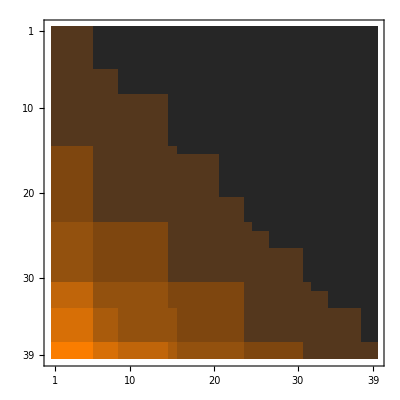
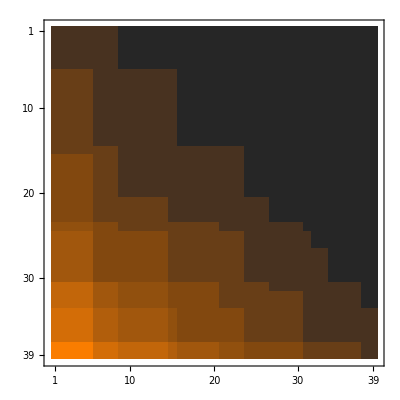
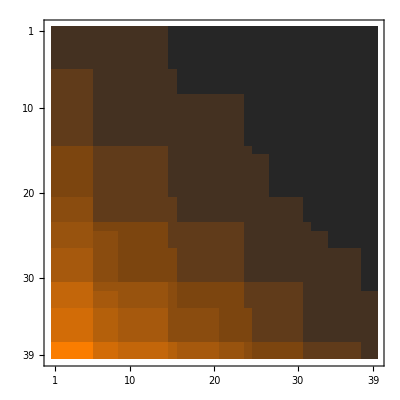
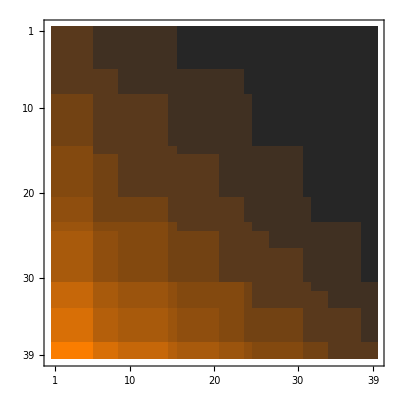
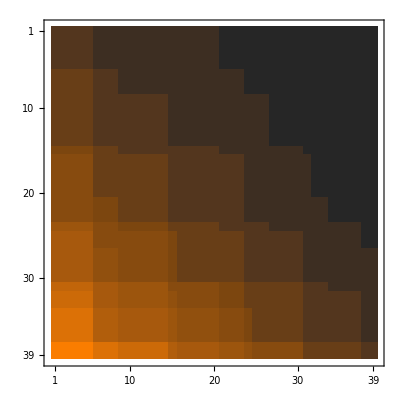
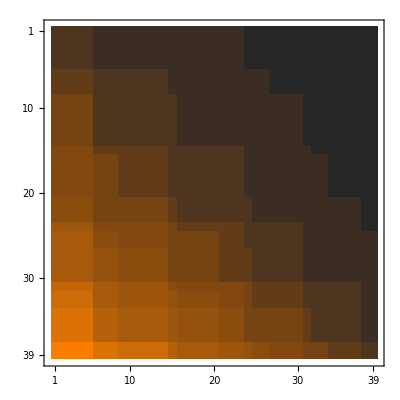
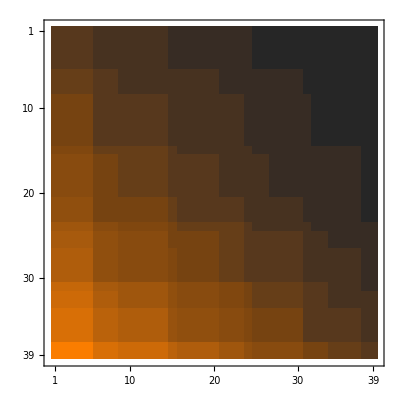
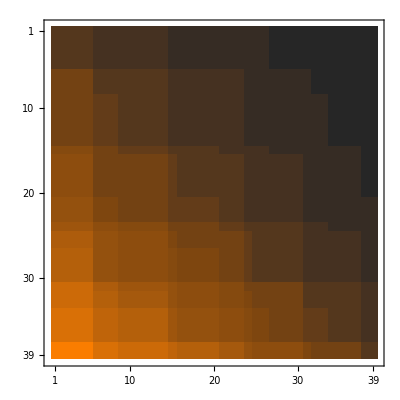
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
B=Array[Floor@N[qdim[[#1]]qdim[[#2]]/qdim[[#3]]] &, {r,r,r}];
MatrixPlot /@B
```

```mathematica
traces
```

{{1,1,0,-1,-1,2,0,1,1,0,-2,0,2,0,2,-1,-1,0,-1,-1,1,1,1,1,2,0,2,-1,-1,0,1,1,2,1,1,1,1,1,1},{1,-1,0,1,-1,0,0,1,-1,0,0,0,0,0,0,1,-1,0,-1,1,-1,1,1,-1,0,0,0,-1,1,0,-1,1,0,-1,1,1,-1,-1,1},{1,1,-2,1,1,2,-2,1,1,-2,2,-2,2,-2,2,1,1,-2,1,1,1,1,1,1,2,-2,2,1,1,-2,1,1,2,1,1,1,1,1,1},{1,1,2,1,1,2,2,1,1,2,2,2,2,2,2,1,1,2,1,1,1,1,1,1,2,2,2,1,1,2,1,1,2,1,1,1,1,1,1},{1,-1,0,-1,1,0,0,1,-1,0,0,0,0,0,0,-1,1,0,1,-1,-1,1,1,-1,0,0,0,1,-1,0,-1,1,0,-1,1,1,-1,-1,1},{√2,√2,√2,0,0,0,-√2,-√2,-√2,√2,0,-√2,2 √2,√2,0,0,0,√2,0,0,-√2,-√2,√2,√2,0,-√2,-2 √2,0,0,-√2,√2,√2,0,√2,√2,-√2,-√2,-√2,-√2},{√2,√2,-√2,0,0,0,√2,-√2,-√2,-√2,0,√2,2 √2,-√2,0,0,0,-√2,0,0,-√2,-√2,√2,√2,0,√2,-2 √2,0,0,√2,√2,√2,0,√2,√2,-√2,-√2,-√2,-√2},{√2,-√2,0,0,0,0,0,-√2,√2,0,0,0,0,0,0,0,0,0,0,0,√2,-√2,√2,-√2,0,0,0,0,0,0,-√2,√2,0,-√2,√2,-√2,√2,√2,-√2},{1/2 (1+√5),1/2 (1+√5),√5,1/2 (-1+√5),1/2 (-1+√5),1,0,1/2 (1-√5),1/2 (1-√5),0,-1,-√5,1,0,1-√5,1/2 (-1-√5),1/2 (-1-√5),-√5,1/2 (-1+√5),1/2 (-1+√5),1/2 (1-√5),1/2 (1-√5),1/2 (1-√5),1/2 (1-√5),1+√5,√5,1,1/2 (-1-√5),1/2 (-1-√5),0,1/2 (1+√5),1/2 (1+√5),1,1/2 (1-√5),1/2 (1-√5),1/2 (1+√5),1/2 (1+√5),1/2 (1+√5),1/2 (1+√5)},{1/2 (1+√5),1/2 (1+√5),-√5,1/2 (-1+√5),1/2 (-1+√5),1,0,1/2 (1-√5),1/2 (1-√5),0,-1,√5,1,0,1-√5,1/2 (-1-√5),1/2 (-1-√5),√5,1/2 (-1+√5),1/2 (-1+√5),1/2 (1-√5),1/2 (1-√5),1/2 (1-√5),1/2 (1-√5),1+√5,-√5,1,1/2 (-1-√5),1/2 (-1-√5),0,1/2 (1+√5),1/2 (1+√5),1,1/2 (1-√5),1/2 (1-√5),1/2 (1+√5),1/2 (1+√5),1/2 (1+√5),1/2 (1+√5)},{1/2 (1+√5),1/2 (-1-√5),0,1/2 (1-√5),1/2 (-1+√5),0,0,1/2 (1-√5),1/2 (-1+√5),0,0,0,0,0,0,1/2 (1+√5),1/2 (-1-√5),0,1/2 (-1+√5),1/2 (1-√5),1/2 (-1+√5),1/2 (1-√5),1/2 (1-√5),1/2 (-1+√5),0,0,0,1/2 (-1-√5),1/2 (1+√5),0,1/2 (-1-√5),1/2 (1+√5),0,1/2 (-1+√5),1/2 (1-√5),1/2 (1+√5),1/2 (-1-√5),1/2 (-1-√5),1/2 (1+√5)},{1/2 (1+√5),1/2 (1+√5),1,1/2 (1-√5),1/2 (1-√5),1,1-√5,1/2 (1-√5),1/2 (1-√5),1+√5,1,1,1,1-√5,1-√5,1/2 (1+√5),1/2 (1+√5),1,1/2 (1-√5),1/2 (1-√5),1/2 (1-√5),1/2 (1-√5),1/2 (1-√5),1/2 (1-√5),1+√5,1,1,1/2 (1+√5),1/2 (1+√5),1+√5,1/2 (1+√5),1/2 (1+√5),1,1/2 (1-√5),1/2 (1-√5),1/2 (1+√5),1/2 (1+√5),1/2 (1+√5),1/2 (1+√5)},{1/2 (1+√5),1/2 (1+√5),-1,1/2 (1-√5),1/2 (1-√5),1,-1+√5,1/2 (1-√5),1/2 (1-√5),-1-√5,1,-1,1,-1+√5,1-√5,1/2 (1+√5),1/2 (1+√5),-1,1/2 (1-√5),1/2 (1-√5),1/2 (1-√5),1/2 (1-√5),1/2 (1-√5),1/2 (1-√5),1+√5,-1,1,1/2 (1+√5),1/2 (1+√5),-1-√5,1/2 (1+√5),1/2 (1+√5),1,1/2 (1-√5),1/2 (1-√5),1/2 (1+√5),1/2 (1+√5),1/2 (1+√5),1/2 (1+√5)},{1/2 (1+√5),1/2 (-1-√5),0,1/2 (-1+√5),1/2 (1-√5),0,0,1/2 (1-√5),1/2 (-1+√5),0,0,0,0,0,0,1/2 (-1-√5),1/2 (1+√5),0,1/2 (1-√5),1/2 (-1+√5),1/2 (-1+√5),1/2 (1-√5),1/2 (1-√5),1/2 (-1+√5),0,0,0,1/2 (1+√5),1/2 (-1-√5),0,1/2 (-1-√5),1/2 (1+√5),0,1/2 (-1+√5),1/2 (1-√5),1/2 (1+√5),1/2 (-1-√5),1/2 (-1-√5),1/2 (1+√5)},{2,2,0,0,0,-4,0,2,2,0,0,0,4,0,-4,0,0,0,0,0,2,2,2,2,-4,0,4,0,0,0,2,2,-4,2,2,2,2,2,2},{√(3+√5),√(3+√5),-√(3-√5),0,0,-√10,√(3-√5),√(3-√5),√(3-√5),√(3+√5),0,-√(3+√5),√2,-√(3-√5),0,0,0,√(3+√5),0,0,√(3-√5),√(3-√5),-√(3-√5),-√(3-√5),0,√(3-√5),-√2,0,0,-√(3+√5),√(3+√5),√(3+√5),√10,-√(3-√5),-√(3-√5),-√(3+√5),-√(3+√5),-√(3+√5),-√(3+√5)},{√(3+√5),√(3+√5),-√(3+√5),0,0,√10,-√(3-√5),√(3-√5),√(3-√5),-√(3+√5),0,-√(3-√5),√2,√(3-√5),0,0,0,√(3-√5),0,0,√(3-√5),√(3-√5),-√(3-√5),-√(3-√5),0,√(3+√5),-√2,0,0,√(3+√5),√(3+√5),√(3+√5),-√10,-√(3-√5),-√(3-√5),-√(3+√5),-√(3+√5),-√(3+√5),-√(3+√5)},{√(3+√5),√(3+√5),√(3+√5),0,0,√10,√(3-√5),√(3-√5),√(3-√5),√(3+√5),0,√(3-√5),√2,-√(3-√5),0,0,0,-√(3-√5),0,0,√(3-√5),√(3-√5),-√(3-√5),-√(3-√5),0,-√(3+√5),-√2,0,0,-√(3+√5),√(3+√5),√(3+√5),-√10,-√(3-√5),-√(3-√5),-√(3+√5),-√(3+√5),-√(3+√5),-√(3+√5)},{√(3+√5),√(3+√5),√(3-√5),0,0,-√10,-√(3-√5),√(3-√5),√(3-√5),-√(3+√5),0,√(3+√5),√2,√(3-√5),0,0,0,-√(3+√5),0,0,√(3-√5),√(3-√5),-√(3-√5),-√(3-√5),0,-√(3-√5),-√2,0,0,√(3+√5),√(3+√5),√(3+√5),√10,-√(3-√5),-√(3-√5),-√(3+√5),-√(3+√5),-√(3+√5),-√(3+√5)},{√(3+√5),-√(3+√5),0,0,0,0,0,√(3-√5),-√(3-√5),0,0,0,0,0,0,0,0,0,0,0,-√(3-√5),√(3-√5),-√(3-√5),√(3-√5),0,0,0,0,0,0,-√(3+√5),√(3+√5),0,√(3-√5),-√(3-√5),-√(3+√5),√(3+√5),√(3+√5),-√(3+√5)},{1/2 (3+√5),1/2 (3+√5),0,1/2 (-3+√5),1/2 (-3+√5),-2,0,1/2 (3-√5),1/2 (3-√5),0,2,0,-2,0,3-√5,1/2 (-3-√5),1/2 (-3-√5),0,1/2 (-3+√5),1/2 (-3+√5),1/2 (3-√5),1/2 (3-√5),1/2 (3-√5),1/2 (3-√5),3+√5,0,-2,1/2 (-3-√5),1/2 (-3-√5),0,1/2 (3+√5),1/2 (3+√5),-2,1/2 (3-√5),1/2 (3-√5),1/2 (3+√5),1/2 (3+√5),1/2 (3+√5),1/2 (3+√5)},{1/2 (3+√5),1/2 (3+√5),-2,1/2 (3-√5),1/2 (3-√5),-2,3-√5,1/2 (3-√5),1/2 (3-√5),3+√5,-2,-2,-2,3-√5,3-√5,1/2 (3+√5),1/2 (3+√5),-2,1/2 (3-√5),1/2 (3-√5),1/2 (3-√5),1/2 (3-√5),1/2 (3-√5),1/2 (3-√5),3+√5,-2,-2,1/2 (3+√5),1/2 (3+√5),3+√5,1/2 (3+√5),1/2 (3+√5),-2,1/2 (3-√5),1/2 (3-√5),1/2 (3+√5),1/2 (3+√5),1/2 (3+√5),1/2 (3+√5)},{1/2 (3+√5),1/2 (3+√5),2,1/2 (3-√5),1/2 (3-√5),-2,-3+√5,1/2 (3-√5),1/2 (3-√5),-3-√5,-2,2,-2,-3+√5,3-√5,1/2 (3+√5),1/2 (3+√5),2,1/2 (3-√5),1/2 (3-√5),1/2 (3-√5),1/2 (3-√5),1/2 (3-√5),1/2 (3-√5),3+√5,2,-2,1/2 (3+√5),1/2 (3+√5),-3-√5,1/2 (3+√5),1/2 (3+√5),-2,1/2 (3-√5),1/2 (3-√5),1/2 (3+√5),1/2 (3+√5),1/2 (3+√5),1/2 (3+√5)},{1+√5,1+√5,0,0,0,-2,0,1-√5,1-√5,0,0,0,2,0,-2+2 √5,0,0,0,0,0,1-√5,1-√5,1-√5,1-√5,-2-2 √5,0,2,0,0,0,1+√5,1+√5,-2,1-√5,1-√5,1+√5,1+√5,1+√5,1+√5},{√(7+3 √5),√(7+3 √5),√2,0,0,0,√(7-3 √5),-√(7-3 √5),-√(7-3 √5),-√(7+3 √5),0,-√2,-2 √2,-√(7-3 √5),0,0,0,√2,0,0,-√(7-3 √5),-√(7-3 √5),√(7-3 √5),√(7-3 √5),0,-√2,2 √2,0,0,√(7+3 √5),√(7+3 √5),√(7+3 √5),0,√(7-3 √5),√(7-3 √5),-√(7+3 √5),-√(7+3 √5),-√(7+3 √5),-√(7+3 √5)},{√(7+3 √5),√(7+3 √5),-√2,0,0,0,-√(7-3 √5),-√(7-3 √5),-√(7-3 √5),√(7+3 √5),0,√2,-2 √2,√(7-3 √5),0,0,0,-√2,0,0,-√(7-3 √5),-√(7-3 √5),√(7-3 √5),√(7-3 √5),0,√2,2 √2,0,0,-√(7+3 √5),√(7+3 √5),√(7+3 √5),0,√(7-3 √5),√(7-3 √5),-√(7+3 √5),-√(7+3 √5),-√(7+3 √5),-√(7+3 √5)},{√(2 (5+√5)),-√(2 (5+√5)),0,-√(5-√5),√(5-√5),0,0,√(2 (5-√5)),-√(2 (5-√5)),0,0,0,0,0,0,-√(5+√5),√(5+√5),0,-√(5-√5),√(5-√5),√(2 (5-√5)),-√(2 (5-√5)),√(2 (5-√5)),-√(2 (5-√5)),0,0,0,-√(5+√5),√(5+√5),0,√(2 (5+√5)),-√(2 (5+√5)),0,√(2 (5-√5)),-√(2 (5-√5)),√(2 (5+√5)),-√(2 (5+√5)),√(2 (5+√5)),-√(2 (5+√5))},{√(2 (5+√5)),-√(2 (5+√5)),0,√(5-√5),-√(5-√5),0,0,√(2 (5-√5)),-√(2 (5-√5)),0,0,0,0,0,0,√(5+√5),-√(5+√5),0,√(5-√5),-√(5-√5),√(2 (5-√5)),-√(2 (5-√5)),√(2 (5-√5)),-√(2 (5-√5)),0,0,0,√(5+√5),-√(5+√5),0,√(2 (5+√5)),-√(2 (5+√5)),0,√(2 (5-√5)),-√(2 (5-√5)),√(2 (5+√5)),-√(2 (5+√5)),√(2 (5+√5)),-√(2 (5+√5))},{√(2 (5+√5)),√(2 (5+√5)),0,√(5-√5),√(5-√5),0,0,√(2 (5-√5)),√(2 (5-√5)),0,0,0,0,0,0,√(5+√5),√(5+√5),0,-√(5-√5),-√(5-√5),-√(2 (5-√5)),-√(2 (5-√5)),√(2 (5-√5)),√(2 (5-√5)),0,0,0,-√(5+√5),-√(5+√5),0,-√(2 (5+√5)),-√(2 (5+√5)),0,-√(2 (5-√5)),-√(2 (5-√5)),√(2 (5+√5)),√(2 (5+√5)),-√(2 (5+√5)),-√(2 (5+√5))},{√(2 (5+√5)),√(2 (5+√5)),0,-√(5-√5),-√(5-√5),0,0,√(2 (5-√5)),√(2 (5-√5)),0,0,0,0,0,0,-√(5+√5),-√(5+√5),0,√(5-√5),√(5-√5),-√(2 (5-√5)),-√(2 (5-√5)),√(2 (5-√5)),√(2 (5-√5)),0,0,0,√(5+√5),√(5+√5),0,-√(2 (5+√5)),-√(2 (5+√5)),0,-√(2 (5-√5)),-√(2 (5-√5)),√(2 (5+√5)),√(2 (5+√5)),-√(2 (5+√5)),-√(2 (5+√5))},{3+√5,3+√5,0,0,0,4,0,3-√5,3-√5,0,0,0,-4,0,-6+2 √5,0,0,0,0,0,3-√5,3-√5,3-√5,3-√5,-6-2 √5,0,-4,0,0,0,3+√5,3+√5,4,3-√5,3-√5,3+√5,3+√5,3+√5,3+√5},{2 √(5+√5),-2 √(5+√5),0,0,0,0,0,-2 √(5-√5),2 √(5-√5),0,0,0,0,0,0,0,0,0,0,0,-2 √(5-√5),2 √(5-√5),2 √(5-√5),-2 √(5-√5),0,0,0,0,0,0,2 √(5+√5),-2 √(5+√5),0,2 √(5-√5),-2 √(5-√5),-2 √(5+√5),2 √(5+√5),-2 √(5+√5),2 √(5+√5)},{2 √(5+√5),2 √(5+√5),0,0,0,0,0,-2 √(5-√5),-2 √(5-√5),0,0,0,0,0,0,0,0,0,0,0,2 √(5-√5),2 √(5-√5),2 √(5-√5),2 √(5-√5),0,0,0,0,0,0,-2 √(5+√5),-2 √(5+√5),0,-2 √(5-√5),-2 √(5-√5),-2 √(5+√5),-2 √(5+√5),2 √(5+√5),2 √(5+√5)},{2 √(5+2 √5),2 √(5+2 √5),0,-√(2 (5-2 √5)),-√(2 (5-2 √5)),0,0,-2 √(5-2 √5),-2 √(5-2 √5),0,0,0,0,0,0,√(2 (5+2 √5)),√(2 (5+2 √5)),0,√(2 (5-2 √5)),√(2 (5-2 √5)),2 √(5-2 √5),2 √(5-2 √5),-2 √(5-2 √5),-2 √(5-2 √5),0,0,0,-√(2 (5+2 √5)),-√(2 (5+2 √5)),0,-2 √(5+2 √5),-2 √(5+2 √5),0,2 √(5-2 √5),2 √(5-2 √5),2 √(5+2 √5),2 √(5+2 √5),-2 √(5+2 √5),-2 √(5+2 √5)},{2 √(5+2 √5),2 √(5+2 √5),0,√(2 (5-2 √5)),√(2 (5-2 √5)),0,0,-2 √(5-2 √5),-2 √(5-2 √5),0,0,0,0,0,0,-√(2 (5+2 √5)),-√(2 (5+2 √5)),0,-√(2 (5-2 √5)),-√(2 (5-2 √5)),2 √(5-2 √5),2 √(5-2 √5),-2 √(5-2 √5),-2 √(5-2 √5),0,0,0,√(2 (5+2 √5)),√(2 (5+2 √5)),0,-2 √(5+2 √5),-2 √(5+2 √5),0,2 √(5-2 √5),2 √(5-2 √5),2 √(5+2 √5),2 √(5+2 √5),-2 √(5+2 √5),-2 √(5+2 √5)},{2 √(5+2 √5),-2 √(5+2 √5),0,√(2 (5-2 √5)),-√(2 (5-2 √5)),0,0,-2 √(5-2 √5),2 √(5-2 √5),0,0,0,0,0,0,-√(2 (5+2 √5)),√(2 (5+2 √5)),0,√(2 (5-2 √5)),-√(2 (5-2 √5)),-2 √(5-2 √5),2 √(5-2 √5),-2 √(5-2 √5),2 √(5-2 √5),0,0,0,-√(2 (5+2 √5)),√(2 (5+2 √5)),0,2 √(5+2 √5),-2 √(5+2 √5),0,-2 √(5-2 √5),2 √(5-2 √5),2 √(5+2 √5),-2 √(5+2 √5),2 √(5+2 √5),-2 √(5+2 √5)},{2 √(5+2 √5),-2 √(5+2 √5),0,-√(2 (5-2 √5)),√(2 (5-2 √5)),0,0,-2 √(5-2 √5),2 √(5-2 √5),0,0,0,0,0,0,√(2 (5+2 √5)),-√(2 (5+2 √5)),0,-√(2 (5-2 √5)),√(2 (5-2 √5)),-2 √(5-2 √5),2 √(5-2 √5),-2 √(5-2 √5),2 √(5-2 √5),0,0,0,√(2 (5+2 √5)),-√(2 (5+2 √5)),0,2 √(5+2 √5),-2 √(5+2 √5),0,-2 √(5-2 √5),2 √(5-2 √5),2 √(5+2 √5),-2 √(5+2 √5),2 √(5+2 √5),-2 √(5+2 √5)},{2 √(2 (5+2 √5)),-2 √(2 (5+2 √5)),0,0,0,0,0,2 √(2 (5-2 √5)),-2 √(2 (5-2 √5)),0,0,0,0,0,0,0,0,0,0,0,2 √(2 (5-2 √5)),-2 √(2 (5-2 √5)),-2 √(2 (5-2 √5)),2 √(2 (5-2 √5)),0,0,0,0,0,0,2 √(2 (5+2 √5)),-2 √(2 (5+2 √5)),0,-2 √(2 (5-2 √5)),2 √(2 (5-2 √5)),-2 √(2 (5+2 √5)),2 √(2 (5+2 √5)),-2 √(2 (5+2 √5)),2 √(2 (5+2 √5))},{2 √(2 (5+2 √5)),2 √(2 (5+2 √5)),0,0,0,0,0,2 √(2 (5-2 √5)),2 √(2 (5-2 √5)),0,0,0,0,0,0,0,0,0,0,0,-2 √(2 (5-2 √5)),-2 √(2 (5-2 √5)),-2 √(2 (5-2 √5)),-2 √(2 (5-2 √5)),0,0,0,0,0,0,-2 √(2 (5+2 √5)),-2 √(2 (5+2 √5)),0,2 √(2 (5-2 √5)),2 √(2 (5-2 √5)),-2 √(2 (5+2 √5)),-2 √(2 (5+2 √5)),2 √(2 (5+2 √5)),2 √(2 (5+2 √5))}}

```mathematica
AA=Select[traces//Transpose,#[[4]]!=2&];
vals=Union[Flatten[AA]];
field=ToNumberField[vals,All];
A=AA/. Thread[vals->field];
x=Array[x,r];
F= [A];
```

LinearSolve::sqmat1: The matrix {«1»} is not square, so a factorization will not be saved.

```mathematica
{i,j}={38,4};
b=A[[All,i]]*A[[All,j]];
M=B[[i,j]];
F[b]//Chop//Rationalize//Time
x/.#& /@Solve[Thread[A . x == b]~Join~Thread[ 0<= x <= M],x,Integers]
```

Time:   0.000319

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0}

{{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0}}

```mathematica
A//FullSimplify//MatrixForm
```

(1 | 1 | 1 | 1 | 1 | √2 | √2 | √2 | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 2 | √(3+√5) | √(3+√5) | √(3+√5) | √(3+√5) | √(3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1+√5 | √(7+3 √5) | √(7+3 √5) | √(2 (5+√5)) | √(2 (5+√5)) | √(2 (5+√5)) | √(2 (5+√5)) | 3+√5 | 2 √(5+√5) | 2 √(5+√5) | 2 √(5+2 √5) | 2 √(5+2 √5) | 2 √(5+2 √5) | 2 √(5+2 √5) | 2 √(10+4 √5) | 2 √(10+4 √5)
1 | -1 | 1 | 1 | -1 | √2 | √2 | -√2 | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (-1-√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (-1-√5) | 2 | √(3+√5) | √(3+√5) | √(3+√5) | √(3+√5) | -√(3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1+√5 | √(7+3 √5) | √(7+3 √5) | -√(2 (5+√5)) | -√(2 (5+√5)) | √(2 (5+√5)) | √(2 (5+√5)) | 3+√5 | -2 √(5+√5) | 2 √(5+√5) | 2 √(5+2 √5) | 2 √(5+2 √5) | -2 √(5+2 √5) | -2 √(5+2 √5) | -2 √(10+4 √5) | 2 √(10+4 √5)
-1 | 1 | 1 | 1 | -1 | 0 | 0 | 0 | 1/2 (-1+√5) | 1/2 (-1+√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (-1+√5) | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 (-3+√5) | 1/2 (3-√5) | 1/2 (3-√5) | 0 | 0 | 0 | -√(5-√5) | √(5-√5) | √(5-√5) | -√(5-√5) | 0 | 0 | 0 | -√(10-4 √5) | √(10-4 √5) | √(10-4 √5) | -√(10-4 √5) | 0 | 0
-1 | -1 | 1 | 1 | 1 | 0 | 0 | 0 | 1/2 (-1+√5) | 1/2 (-1+√5) | 1/2 (-1+√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 (-3+√5) | 1/2 (3-√5) | 1/2 (3-√5) | 0 | 0 | 0 | √(5-√5) | -√(5-√5) | √(5-√5) | -√(5-√5) | 0 | 0 | 0 | -√(10-4 √5) | √(10-4 √5) | -√(10-4 √5) | √(10-4 √5) | 0 | 0
1 | 1 | 1 | 1 | 1 | -√2 | -√2 | -√2 | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 2 | √(3-√5) | √(3-√5) | √(3-√5) | √(3-√5) | √(3-√5) | 1/2 (3-√5) | 1/2 (3-√5) | 1/2 (3-√5) | 1-√5 | (-3+√5)/(√2) | (-3+√5)/(√2) | √(10-2 √5) | √(10-2 √5) | √(10-2 √5) | √(10-2 √5) | 3-√5 | -2 √(5-√5) | -2 √(5-√5) | -2 √(5-2 √5) | -2 √(5-2 √5) | -2 √(5-2 √5) | -2 √(5-2 √5) | 2 √(10-4 √5) | 2 √(10-4 √5)
1 | -1 | 1 | 1 | -1 | -√2 | -√2 | √2 | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (-1+√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (-1+√5) | 2 | √(3-√5) | √(3-√5) | √(3-√5) | √(3-√5) |  | 1/2 (3-√5) | 1/2 (3-√5) | 1/2 (3-√5) | 1-√5 | (-3+√5)/(√2) | (-3+√5)/(√2) | -√(10-2 √5) | -√(10-2 √5) | √(10-2 √5) | √(10-2 √5) | 3-√5 | 2 √(5-√5) | -2 √(5-√5) | -2 √(5-2 √5) | -2 √(5-2 √5) | 2 √(5-2 √5) | 2 √(5-2 √5) | -2 √(10-4 √5) | 2 √(10-4 √5)
-1 | 1 | 1 | 1 | -1 | 0 | 0 | 0 | 1/2 (-1-√5) | 1/2 (-1-√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (-1-√5) | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 (-3-√5) | 1/2 (3+√5) | 1/2 (3+√5) | 0 | 0 | 0 | -√(5+√5) | √(5+√5) | √(5+√5) | -√(5+√5) | 0 | 0 | 0 | √(10+4 √5) | -√(10+4 √5) | -√(10+4 √5) | √(10+4 √5) | 0 | 0
-1 | -1 | 1 | 1 | 1 | 0 | 0 | 0 | 1/2 (-1-√5) | 1/2 (-1-√5) | 1/2 (-1-√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 (-3-√5) | 1/2 (3+√5) | 1/2 (3+√5) | 0 | 0 | 0 | √(5+√5) | -√(5+√5) | √(5+√5) | -√(5+√5) | 0 | 0 | 0 | √(10+4 √5) | -√(10+4 √5) | √(10+4 √5) | -√(10+4 √5) | 0 | 0
-1 | -1 | 1 | 1 | 1 | 0 | 0 | 0 | 1/2 (-1+√5) | 1/2 (-1+√5) | 1/2 (-1+√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 (-3+√5) | 1/2 (3-√5) | 1/2 (3-√5) | 0 | 0 | 0 | -√(5-√5) | √(5-√5) | -√(5-√5) | √(5-√5) | 0 | 0 | 0 | √(10-4 √5) | -√(10-4 √5) | √(10-4 √5) | -√(10-4 √5) | 0 | 0
-1 | 1 | 1 | 1 | -1 | 0 | 0 | 0 | 1/2 (-1+√5) | 1/2 (-1+√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (-1+√5) | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 (-3+√5) | 1/2 (3-√5) | 1/2 (3-√5) | 0 | 0 | 0 | √(5-√5) | -√(5-√5) | -√(5-√5) | √(5-√5) | 0 | 0 | 0 | √(10-4 √5) | -√(10-4 √5) | -√(10-4 √5) | √(10-4 √5) | 0 | 0
1 | -1 | 1 | 1 | -1 | -√2 | -√2 | √2 | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (-1+√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (-1+√5) | 2 | √(3-√5) | √(3-√5) | √(3-√5) | √(3-√5) |  | 1/2 (3-√5) | 1/2 (3-√5) | 1/2 (3-√5) | 1-√5 | (-3+√5)/(√2) | (-3+√5)/(√2) | √(10-2 √5) | √(10-2 √5) | -√(10-2 √5) | -√(10-2 √5) | 3-√5 | -2 √(5-√5) | 2 √(5-√5) | 2 √(5-2 √5) | 2 √(5-2 √5) | -2 √(5-2 √5) | -2 √(5-2 √5) | 2 √(10-4 √5) | -2 √(10-4 √5)
1 | 1 | 1 | 1 | 1 | -√2 | -√2 | -√2 | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 2 | √(3-√5) | √(3-√5) | √(3-√5) | √(3-√5) | √(3-√5) | 1/2 (3-√5) | 1/2 (3-√5) | 1/2 (3-√5) | 1-√5 | (-3+√5)/(√2) | (-3+√5)/(√2) | -√(10-2 √5) | -√(10-2 √5) | -√(10-2 √5) | -√(10-2 √5) | 3-√5 | 2 √(5-√5) | 2 √(5-√5) | 2 √(5-2 √5) | 2 √(5-2 √5) | 2 √(5-2 √5) | 2 √(5-2 √5) | -2 √(10-4 √5) | -2 √(10-4 √5)
1 | 1 | 1 | 1 | 1 | √2 | √2 | √2 | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 2 |  |  |  |  |  | 1/2 (3-√5) | 1/2 (3-√5) | 1/2 (3-√5) | 1-√5 | √(7-3 √5) | √(7-3 √5) | √(10-2 √5) | √(10-2 √5) | √(10-2 √5) | √(10-2 √5) | 3-√5 | 2 √(5-√5) | 2 √(5-√5) | -2 √(5-2 √5) | -2 √(5-2 √5) | -2 √(5-2 √5) | -2 √(5-2 √5) | -2 √(10-4 √5) | -2 √(10-4 √5)
1 | -1 | 1 | 1 | -1 | √2 | √2 | -√2 | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (-1+√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (-1+√5) | 2 |  |  |  |  | √(3-√5) | 1/2 (3-√5) | 1/2 (3-√5) | 1/2 (3-√5) | 1-√5 | √(7-3 √5) | √(7-3 √5) | -√(10-2 √5) | -√(10-2 √5) | √(10-2 √5) | √(10-2 √5) | 3-√5 | -2 √(5-√5) | 2 √(5-√5) | -2 √(5-2 √5) | -2 √(5-2 √5) | 2 √(5-2 √5) | 2 √(5-2 √5) | 2 √(10-4 √5) | -2 √(10-4 √5)
-1 | -1 | 1 | 1 | 1 | 0 | 0 | 0 | 1/2 (-1-√5) | 1/2 (-1-√5) | 1/2 (-1-√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 (-3-√5) | 1/2 (3+√5) | 1/2 (3+√5) | 0 | 0 | 0 | -√(5+√5) | √(5+√5) | -√(5+√5) | √(5+√5) | 0 | 0 | 0 | -√(10+4 √5) | √(10+4 √5) | -√(10+4 √5) | √(10+4 √5) | 0 | 0
-1 | 1 | 1 | 1 | -1 | 0 | 0 | 0 | 1/2 (-1-√5) | 1/2 (-1-√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (-1-√5) | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 (-3-√5) | 1/2 (3+√5) | 1/2 (3+√5) | 0 | 0 | 0 | √(5+√5) | -√(5+√5) | -√(5+√5) | √(5+√5) | 0 | 0 | 0 | -√(10+4 √5) | √(10+4 √5) | √(10+4 √5) | -√(10+4 √5) | 0 | 0
1 | -1 | 1 | 1 | -1 | √2 | √2 | -√2 | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (-1-√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (-1-√5) | 2 | √(3+√5) | √(3+√5) | √(3+√5) | √(3+√5) | -√(3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1+√5 | √(7+3 √5) | √(7+3 √5) | √(2 (5+√5)) | √(2 (5+√5)) | -√(2 (5+√5)) | -√(2 (5+√5)) | 3+√5 | 2 √(5+√5) | -2 √(5+√5) | -2 √(5+2 √5) | -2 √(5+2 √5) | 2 √(5+2 √5) | 2 √(5+2 √5) | 2 √(10+4 √5) | -2 √(10+4 √5)
1 | 1 | 1 | 1 | 1 | √2 | √2 | √2 | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 2 | √(3+√5) | √(3+√5) | √(3+√5) | √(3+√5) | √(3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1+√5 | √(7+3 √5) | √(7+3 √5) | -√(2 (5+√5)) | -√(2 (5+√5)) | -√(2 (5+√5)) | -√(2 (5+√5)) | 3+√5 | -2 √(5+√5) | -2 √(5+√5) | -2 √(5+2 √5) | -2 √(5+2 √5) | -2 √(5+2 √5) | -2 √(5+2 √5) | -2 √(10+4 √5) | -2 √(10+4 √5)
1 | -1 | 1 | 1 | -1 | √2 | √2 | -√2 | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (-1+√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (-1+√5) | 2 |  |  |  |  | √(3-√5) | 1/2 (3-√5) | 1/2 (3-√5) | 1/2 (3-√5) | 1-√5 | √(7-3 √5) | √(7-3 √5) | √(10-2 √5) | √(10-2 √5) | -√(10-2 √5) | -√(10-2 √5) | 3-√5 | 2 √(5-√5) | -2 √(5-√5) | 2 √(5-2 √5) | 2 √(5-2 √5) | -2 √(5-2 √5) | -2 √(5-2 √5) | -2 √(10-4 √5) | 2 √(10-4 √5)
1 | 1 | 1 | 1 | 1 | √2 | √2 | √2 | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 2 |  |  |  |  |  | 1/2 (3-√5) | 1/2 (3-√5) | 1/2 (3-√5) | 1-√5 | √(7-3 √5) | √(7-3 √5) | -√(10-2 √5) | -√(10-2 √5) | -√(10-2 √5) | -√(10-2 √5) | 3-√5 | -2 √(5-√5) | -2 √(5-√5) | 2 √(5-2 √5) | 2 √(5-2 √5) | 2 √(5-2 √5) | 2 √(5-2 √5) | 2 √(10-4 √5) | 2 √(10-4 √5)
1 | 1 | 1 | 1 | 1 | -√2 | -√2 | -√2 | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 2 | -√(3+√5) | -√(3+√5) | -√(3+√5) | -√(3+√5) | -√(3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1+√5 | -√(7+3 √5) | -√(7+3 √5) | √(2 (5+√5)) | √(2 (5+√5)) | √(2 (5+√5)) | √(2 (5+√5)) | 3+√5 | -2 √(5+√5) | -2 √(5+√5) | 2 √(5+2 √5) | 2 √(5+2 √5) | 2 √(5+2 √5) | 2 √(5+2 √5) | -2 √(10+4 √5) | -2 √(10+4 √5)
1 | -1 | 1 | 1 | -1 | -√2 | -√2 | √2 | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (-1-√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (-1-√5) | 2 | -√(3+√5) | -√(3+√5) | -√(3+√5) | -√(3+√5) | √(3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1+√5 | -√(7+3 √5) | -√(7+3 √5) | -√(2 (5+√5)) | -√(2 (5+√5)) | √(2 (5+√5)) | √(2 (5+√5)) | 3+√5 | 2 √(5+√5) | -2 √(5+√5) | 2 √(5+2 √5) | 2 √(5+2 √5) | -2 √(5+2 √5) | -2 √(5+2 √5) | 2 √(10+4 √5) | -2 √(10+4 √5)
1 | -1 | 1 | 1 | -1 | -√2 | -√2 | √2 | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (-1-√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (-1-√5) | 2 | -√(3+√5) | -√(3+√5) | -√(3+√5) | -√(3+√5) | √(3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1+√5 | -√(7+3 √5) | -√(7+3 √5) | √(2 (5+√5)) | √(2 (5+√5)) | -√(2 (5+√5)) | -√(2 (5+√5)) | 3+√5 | -2 √(5+√5) | 2 √(5+√5) | -2 √(5+2 √5) | -2 √(5+2 √5) | 2 √(5+2 √5) | 2 √(5+2 √5) | -2 √(10+4 √5) | 2 √(10+4 √5)
1 | 1 | 1 | 1 | 1 | -√2 | -√2 | -√2 | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 2 | -√(3+√5) | -√(3+√5) | -√(3+√5) | -√(3+√5) | -√(3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1+√5 | -√(7+3 √5) | -√(7+3 √5) | -√(2 (5+√5)) | -√(2 (5+√5)) | -√(2 (5+√5)) | -√(2 (5+√5)) | 3+√5 | 2 √(5+√5) | 2 √(5+√5) | -2 √(5+2 √5) | -2 √(5+2 √5) | -2 √(5+2 √5) | -2 √(5+2 √5) | 2 √(10+4 √5) | 2 √(10+4 √5))

```mathematica
PolynomialCoefficients[x_]:=PolynomialCoefficients[x]=CoefficientList[MinimalPolynomial[x,y],y];
NumericalValue[x_]  := Round[N[x,40]*10^30];
ParseEntry[i_,j_]:=Module[
{coefficients = PolynomialCoefficients[AA[[i,j]]]},
{i,j,Length[coefficients]-1, coefficients, NumericalValue[AA[[i,j]]]}
];
Aexport=Flatten[Array[ParseEntry,Dimensions[AA]],1];//Time
Export[ModuleDirectory<>"fusion/in/A.txt", Aexport]
```

Time:   0.011402

/home/pano/projects/tricritical-ising/bootstrap/scratch/../modules/fusion/in/A.txt

/home/pano/projects/tricritical-ising/bootstrap/scratch/../modules/fusion/in/A.txt